```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts"};
```

```mathematica
Needs["FeynCalc`"]
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
tops = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { F[3,{1}],F[7]} -> {F[3,{1}],F[7]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{S[4],S[1]}, Model ->"./2MDMLO_FA/2MDMLO_FA",GenericModel->"./2MDMLO_FA/2MDMLO_FA_new"];
```

loading generic model file /home/lessa/smodelsv3-paper/models/2MDM/2MDMLO_FA/2MDMLO_FA_new.gen

> $GenericMixing is OFF

generic model {./2MDMLO_FA/2MDMLO_FA_new} initialized

loading classes model file /home/lessa/smodelsv3-paper/models/2MDM/2MDMLO_FA/2MDMLO_FA.mod

> 49 particles (incl. antiparticles) in 21 classes

> $CounterTerms are ON

> 147 vertices

classes model {./2MDMLO_FA/2MDMLO_FA} initialized

Excluding 0 Generic, 2 Classes, and 2 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 2 Classes, and 2 Particles fields

in total: 1 Particles insertion

```mathematica
Paint[allDiags,ColumnsXRows->{1,1},ImageSize->{ 200,200},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

> Top. 1 aebf/cedf/ef.m, 0 diagrams

-Graphics-

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[allDiags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->( M$FACouplings)]/.{GaugeXi[a_]->1}
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

(ⅈ gZp QBq δ_Col1Col3 (φ(OverBar[k1],MU)).(γ̄)^Lor2.(φ(OverBar[p1],MU)) (φ(OverBar[k2],Mchi)).(ⅈ gchi (γ̄)^Lor2.(γ̄)^7-ⅈ gchi (γ̄)^Lor2.(γ̄)^6).(φ(OverBar[p2],Mchi)))/((OverBar[k2]-OverBar[p2])^2-MZp^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MU,Mchi,MU,Mchi];
```

```mathematica
ampSquared[0]=1/4((amp[0] (ComplexConjugate[amp[0]]))//FeynAmpDenominatorExplicit//SUNSimplify[#,Explicit->True,SUNNToCACF->False]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//TrickMandelstam[#,{s,t,u,2 MU^2+2 Mchi^2}]&//Simplify)/.SUNN->3
```

-(6 gchi^2 gZp^2 QBq^2 (4 Mchi^2 MU^2+2 Mchi^4+4 MU^2 (s+u)-6 MU^4-s^2-u^2))/((MZp^2-t)^2)

```mathematica
xsec =1/2 1/(2 Pi)^2(Pi/2 1/s)ampSquared[0]
```

-(3 gchi^2 gZp^2 QBq^2 (4 Mchi^2 MU^2+2 Mchi^4+4 MU^2 (s+u)-6 MU^4-s^2-u^2))/(8 π s (MZp^2-t)^2)

```mathematica
sapp=FullSimplify[Normal[Series[(√(Mchi^2 + Mchi^2 v^2)+MU)^2 - Mchi^2 v^2,{v,0,2}]],Assumptions->{Mchi>0,MU>0}]
```

Mchi MU v^2+(Mchi+MU)^2

```mathematica
xsecSmallMom=Normal[Series[(xsec/.{u->2 MU^2+2 Mchi^2-s-t})//ReplaceAll[#,{ s->sapp,t->0}]&//Simplify,{v,0,2},{MU,0,2}]]//.{QBq->1/3,gchi-> (-2/3 gZp),gZp->gB}
```

(4 gB^4 MU^2 v^2)/(27 π MZp^4)

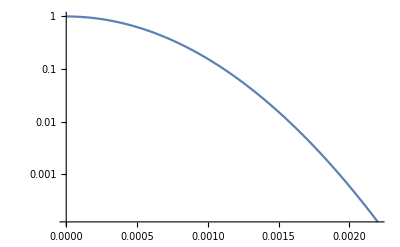

```mathematica
v0=220. 10^3/(3 10^8);
vesc=650. 10^3/(3 10^8);
LogPlot[1/□Exp[-v^2/v0^2],{v,0,3v0}]
```

```mathematica
Integrate[v/V0^3 Exp[-v^2/V0^2],{v,0,Infinity},Assumptions->{V0>0}]
```

1/(2 V0)

```mathematica
v0
```

0.000733333

```mathematica
vesc
```

0.00216667

```mathematica
9.0 (Sin[0.1] Cos[0.1])^2/(Sin[0.2] Cos[0.2])^2
```

2.34246